```mathematica
`
```

# Machine Learning

## Wolfram Data Repository

## Black and White Images

```mathematica
ResourceObject["FER-2013"]
```

ResourceObject[…]

## Color Images

```mathematica
ResourceObject["CIFAR-10"]
```

ResourceObject[…]

## What are Images ?

### A black and white image is described as a matrix, with values 0 to 1

Zero being white and One being black.

```mathematica
blackAndWhite = Table[RandomInteger[1],{i,3},{j,3}] ;
```

```mathematica
TraditionalForm[MatrixForm[blackAndWhite]]
```

(1 | 0 | 0
0 | 0 | 1
1 | 1 | 0)

#### Plotting Matrices

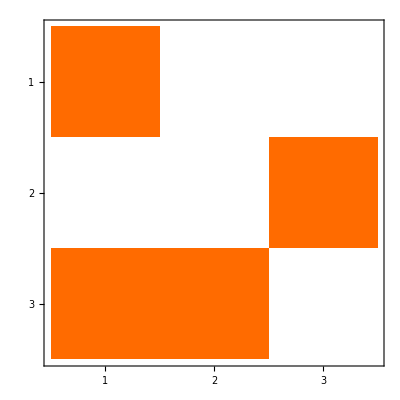

```mathematica
MatrixPlot[blackAndWhite]
```

### Color Images Are Described with Tensors

#### Simple Version

```mathematica
TraditionalForm[MatrixForm[ Table[RandomInteger[1],{i,3},{j,3}]]]
```

(0 | 1 | 0
0 | 0 | 0
1 | 0 | 0)

#### Full Example

```mathematica
colorImage =Table[ Table[RandomInteger[255],{i,3},{j,3}],{i,3},{j,3}];
```

```mathematica
TraditionalForm[MatrixForm[colorImage]]
```

((120 | 231 | 11
239 | 248 | 15
27 | 56 | 192) | (251 | 194 | 90
213 | 155 | 253
203 | 175 | 99) | (126 | 201 | 97
174 | 140 | 128
252 | 60 | 195)
(107 | 142 | 133
121 | 41 | 142
140 | 246 | 205) | (169 | 35 | 97
230 | 163 | 176
137 | 236 | 7) | (225 | 7 | 13
171 | 182 | 119
57 | 96 | 127)
(101 | 252 | 148
169 | 16 | 232
68 | 222 | 11) | (112 | 99 | 54
101 | 199 | 255
201 | 184 | 161) | (217 | 148 | 250
249 | 80 | 193
23 | 54 | 131))

#### A Tensor can be described with a sparse array.

```mathematica
sparse = SparseArray[colorImage]
```

SparseArray[…]

```mathematica
sparse["Properties"]//MatrixForm
```

(AdjacencyLists
Background
ColumnIndices
Density
MatrixColumns
NonzeroValues
PatternArray
Properties
RowPointers)

## Data for our Machine Learning Models

```mathematica
allData =  RandomSample[ResourceData["FER-2013"],500];
```

```mathematica
allColorData = Import[NotebookDirectory[]<>"/data/colorAnimals.m"];
```

### Data Wrangling (Munging)

```mathematica
allColorData⟦1;;5⟧
```

{-Graphics-→deer,-Graphics-→frog,-Graphics-→airplane,-Graphics-→cat,-Graphics-→frog}

Look at the data that we have in our dataset.

```mathematica
DeleteDuplicates[Last[allColorData⟦#⟧]&/@Range[Length[allColorData]]]
```

{deer,frog,airplane,cat,ship,bird,truck,dog,automobile,horse}

#### Restrictions

```mathematica
myRestrictions = {"cat","dog","horse","deer","frog","bird"};
```

```mathematica
g[x_]:=Select[allColorData,Last[#]==x&];
```

```mathematica
readyData = Flatten[g[#]&/@myRestrictions];
```

```mathematica
readyData//Length
```

601

#### Pattern Matching Example

```mathematica
colorImages = Cases[allColorData,HoldPattern[_->#]]&/@myRestrictions;
```

```mathematica
finalColorPrepData = Flatten[colorImages];
```

## Image Processing

```mathematica
A = allData[[1]]
```

-Graphics-→neutral

```mathematica
First[A]
```

-Graphics-

### Image Functions

```mathematica
Animate[Binarize[First[A],r],{r,0,1,0.1}]
```

### List of Image Functions

```mathematica
house = ExampleData[{"TestImage","House"}]
```

-Graphics-

```mathematica
HistogramTransform[house]
```

-Graphics-

```mathematica
ColorQuantize[house,4]//ImageAdjust
```

-Graphics-

```mathematica
EdgeDetect[house]
```

-Graphics-

```mathematica
Animate[ColorQuantize[house,n,Dithering->False]-EdgeDetect[house],{n,1,20,1}]
```

```mathematica
DominantColors[house]
```

{RGBColor[0.6179548174327589, 0.773418730383829, 0.8688828392911802],RGBColor[0.6595244425699881, 0.4271383455568531, 0.39849783908433695],RGBColor[0.4813593607166102, 0.36722117798938353, 0.411243892126088],RGBColor[0.8549496449365236, 0.8970788768716457, 0.8847619654299778],RGBColor[0.41988990431663153, 0.5373913981838716, 0.6481610879401098]}

```mathematica
rawImage = ClusteringComponents[ColorConvert[house,"Grayscale"],3];
```

```mathematica
Manipulate[func[rawImage],{func,{ArrayPlot,MatrixPlot}}]
```

```mathematica
Animate[
Colorize@ClusteringComponents[ColorConvert[house,"Grayscale"],n],{n,1,100,1}]
```

## Analyse

#### Get A Certain Range of Emotions

```mathematica
emotions = {
Entity["Emotion","Happiness::d8973"],
Entity["Emotion","Neutral::7468h"],
Entity["Emotion","Sadness::t2566"],
Entity["Emotion","Anger::bb6bt"],
Entity["Emotion","Surprise::dj3w9"],
Entity["Emotion","Disgust::s4t7h"],
Entity["Emotion","Fear::7k5tk"]
};
```

```mathematica
emotions⟦1⟧ //FullForm
```

Entity["Emotion","Happiness::d8973"]

#### Function for specified Images

```mathematica
images = Cases[allData,HoldPattern[_->#]]&/@emotions;
```

```mathematica
finalPrep = Flatten[images];
```

#### Splitting Data

```mathematica
Length[finalPrep]
```

500

```mathematica
splitter[20]
```

splitter[20]

```mathematica
splitter[x_] := Floor[Length[finalPrep] * x/(100)];
```

```mathematica
randomOrder = RandomSample[allData];
```

Split Data into training set and test set.

```mathematica
trainingData =Take[randomOrder,splitter[80]];
```

```mathematica
testData = Drop[randomOrder,splitter[80]];
```

```mathematica
distribution = PieChart[{Length[trainingData],Length[testData]},ChartLabels->{"Training Data","Test Data"}]
```

-Graphics-

#### Built-in Machine Learning Model

```mathematica
builtIn = Classify["FacialExpression"];
```

#### Build Your Own Classifier

```mathematica
classifier = Classify[trainingData,TargetDevice->"CPU",Method->"GradientBoostedTrees",PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

#### Information about Classifier

```mathematica
Information[classifier]
```

Classifier information
Data type | Image
Number of classes | 7
Accuracy | (11.42.4) %
Method | GradientBoostedTrees
Single evaluation time | 161. ms/example
Batch evaluation speed | 6.99 examples/s
Loss | 1.94 ± 0.0041
Model memory | 993. kB
Training examples used | 400 examples
Training time | 1 31
 |

#### Testing our Classifier Model

```mathematica
testData[[4]]
```

-Graphics-→surprise

```mathematica
classifier[First@testData[[4]]]
```

surprise

```mathematica
classifier[First[testData[[4]]],"TopProbabilities"]
```

{surprise→0.589726,neutral→0.202787,anger→0.11203}

#### Classifier Application

```mathematica
Manipulate[
GraphicsRow[
{
TableForm@classifier[First[testData[[i]]],"TopProbabilities"],
First[testData⟦i⟧],
BarChart[Association@classifier[First[testData⟦i⟧],"TopProbabilities"]]
},ImageSize->Full],
{i,1, Length[testData],1}]
```

#### Get Statistical Information about your classifier

```mathematica
cm= ClassifierMeasurements[classifier,testData]
```

ClassifierMeasurementsObject[…]

#### Using Test Data

```mathematica
cm["Accuracy"]
```

0.34

```mathematica
Manipulate[cm[prop],{{prop,"ConfusionMatrixPlot","Properties"},cm["Properties"]}]
```

## Color Image Example

#### Data Wrangling

```mathematica
allColorData⟦1;;5⟧
```

{-Graphics-→deer,-Graphics-→frog,-Graphics-→airplane,-Graphics-→cat,-Graphics-→frog}

```mathematica
DeleteDuplicates[Last[allColorData⟦#⟧]&/@Range[Length[allColorData]]]
```

{deer,frog,airplane,cat,ship,bird,truck,dog,automobile,horse}

Create groups of specefic....

```mathematica
myRestrictions = {"cat","dog","horse","deer","frog","bird"};
```

```mathematica
colorImages = Cases[allColorData,HoldPattern[_->#]]&/@myRestrictions;
```

```mathematica
finalColorPrepData = Flatten[colorImages];
```

```mathematica
finalTestData = RandomSample[Flatten[colorImages],200];
```

#### Create Classifier

```mathematica
c = Classify[finalColorPrepData]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Image
Number of classes | 6
Accuracy | (77.23.4) %
Method | LogisticRegression
Single evaluation time | 261. ms/example
Batch evaluation speed | 3.11 examples/s
Loss | 0.663 ± 0.059
Model memory | 324. kB
Training examples used | 601 examples
Training time | 3 35
 |

#### Testing Images

```mathematica
testModel= -Graphics-;
```

```mathematica
testCat = -Graphics-;
```

```mathematica
testBird = First[finalColorPrepData⟦Length[finalColorPrepData]⟧]
```

-Graphics-

#### Testing Model

dog

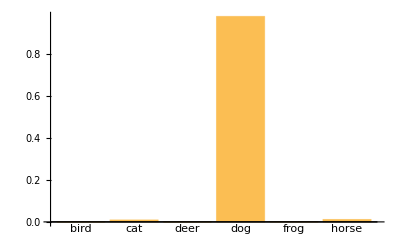

{dog→0.675033,cat→0.302744}

```mathematica
c[testModel] 
BarChart[c[testModel,"Probabilities"],ChartLabels->Automatic]
c[testCat,"TopProbabilities"]
```

```mathematica
c[testBird]
```

bird

#### Measurements

```mathematica
measurements = ClassifierMeasurements[c,finalTestData]
```

ClassifierMeasurementsObject[…]

```mathematica
Manipulate[measurements[x],{x,measurements["Properties"]}]
```